```mathematica
wprim = Function[{a,b,w,k},(a-b*w)k];
kprim = Function[{m,n,k,w},(-m+n*k)w];
```

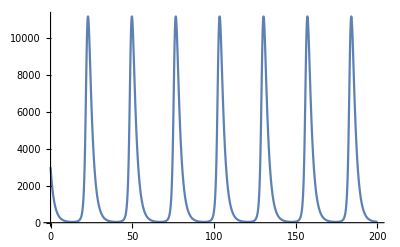

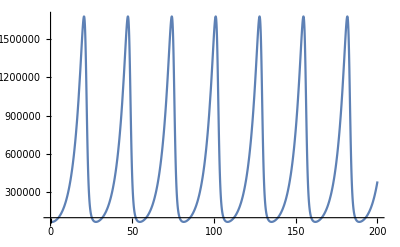

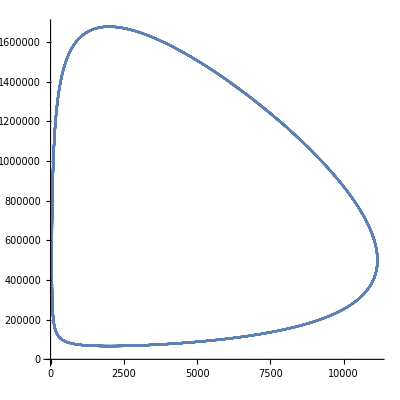

```mathematica
a:=0.2;
b:=0.0001;
m:=0.5;
n:=0.000001;
w0 := 3000;
k0:=70000;
timerange:=200;


s = NDSolve[
{
k'[t]==(a-b*w[t])*k[t],
w'[t]==(-m+n*k[t])*w[t],
w[0]==w0,
k[0]==k0
},{w,k}
,{t,0,timerange}
];

whaleovertime = w/.First@s;
krillovertime = k/.First@s;

whales = Plot[whaleovertime[t],{t,0,timerange}, PlotRange->All]
krill = Plot[krillovertime[t],{t,0,timerange},PlotRange->All]

ParametricPlot[{whaleovertime[t],krillovertime[t]},{t,0,timerange},AspectRatio->1]
```